# Chebyshev coefficients

```mathematica
zerocheb[k_]:=If[k==0,1/2,-2 Sin[π k/2]/(π k) ];
```

```mathematica
Manipulate[Plot[Sum[zerocheb[k] ChebyshevT[k,x],{k,1,num,1}],{x,-1,1}],{num,1,1000,1}]
```

General::munfl: 1/(5.534×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.80701×10^-308+3.177944252256×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.605] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-749.969] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-750.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

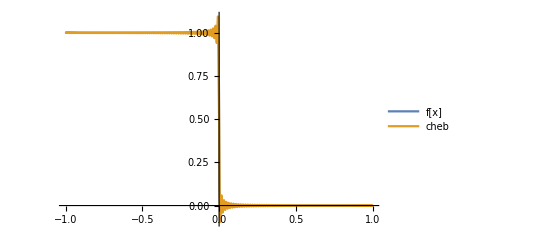

General::munfl: Exp[-749.969] is too small to represent as a normalized machine number; precision may be lost.

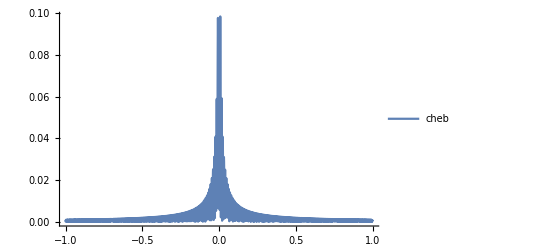

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

579+0.000747727 (-399. x+1.05868×10^7 x^3-8.42667×10^10 x^5+3.19363×10^14 x^7-7.05934×10^17 x^9+285+2.54469×10^126 x^391-1.04393×10^125 x^393+3.18755×10^123 x^395-6.43949×10^121 x^397+6.45562×10^119 x^399)
 |  |  |  |

```mathematica
n=400;
T = 0.01;
Emax = 7.5;

f[x_]= 1/(Exp[Emax/T x]+1);



g1[k_]=((n-k+1) Cos[(π k)/(n+1)]+Sin[(π k)/(n+1)] Cot[π/(n+1)])/(n+1);

λ=0.1;
g2[k_]=Sinh[λ (1-k/n)]/Sinh[λ];

chebTab=Table[(g1[j] 2)/n If[j≠0,1,1/2]Sum[f[Cos[(π (k-1/2))/n]] Cos[(π (k-1/2))/n j],{k,1,n}],{j,0,n-1}];
(*chebTab=Table[zerocheb[j],{j,0,n-1}];*)
cheb[x_]:=Sum[ChebyshevT[k,x]chebTab[[k+1]],{k,0,n-1}];

Plot[{f[x],cheb[x]},{x,-1,1},PlotLegends->{"f[x]","cheb"},PlotRange->All]
Plot[{Abs[cheb[x]-f[x]]},{x,-1,1},PlotLegends->{"cheb"},PlotRange->All]
MaxError = FindMaximum[Abs[cheb[x]-f[x]],{x,-1,1}]
```

```mathematica
H={{h,d},{d,-h}}/.d->0.99/.h->0.0667;
Eigenvalues@H
q[0]={0,1};
q[1]=H.q[0];
Do[q[i+1]=2 H.q[i]-q[i-1],{i,1,1000}]
Sum[q[i][[1]] chebTab[[i+1]],{i,0,999}]
```

{-0.992244,0.992244}

-0.498869

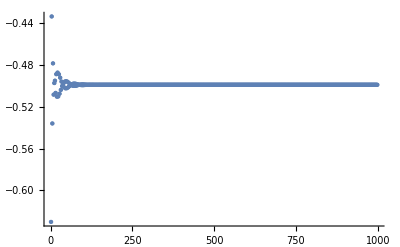

```mathematica
tab=Table[{ord,Sum[q[i][[1]] chebTab[[i+1]],{i,0,ord}]},{ord,1,999}];
ListPlot[tab,PlotRange->All]
```

# 1d exact diagonalization BdG

```mathematica
fac=1.0;

T=0.1;
h=0.0 fac;
n=10;
t[i_]=1.0 fac;
μ0=0.5 fac;
Do[μ[i]=μ0;,{i,n}];
V=2.0 fac;

periodic=0;
hpm[i_,j_,sign_]=(t[i] KroneckerDelta[i,j+1]+Conjugate@t[j] KroneckerDelta[i,j-1]+periodic t[i] (KroneckerDelta[i,1] KroneckerDelta[j,n]+KroneckerDelta[i,n] KroneckerDelta[j,1]))-(μ[i]+sign h) KroneckerDelta[i,j];
d=Table[3.1,{i,n}];
M=Table[0,{i,2 n},{j,2 n}];

Do[M[[i,j]]=N[hpm[i,j,(+1)]],{i,n},{j,n}];
Do[M[[i+n,j+n]]=-Conjugate[N[hpm[i,j,(-1)]]],{i,n},{j,n}];
```

{0.139963,Null}

{{0.002274,-0.002274,-0.00931985,0.00931985,0.0225817,-0.0225817,0.0189882,-0.0189882,-0.0250925,0.0250925,-0.0151742,0.0151742,0.021473,-0.021473,0.0569564,-0.0569564,0.0311487,-0.0311487,0.0654509,-0.0654509},{0.0027762,-0.0027762,-0.00767343,0.00767343,0.0067328,-0.0067328,-0.0104523,0.0104523,-0.0217619,0.0217619,-0.0314527,0.0314527,0.0601183,-0.0601183,0.00262353,-0.00262353,0.0496707,-0.0496707,0.000914679,-0.000914679},{0.00841233,-0.00841233,-0.016782,0.016782,0.00798554,-0.00798554,-0.00230202,0.00230202,-0.0135549,0.0135549,-0.00383073,0.00383073,0.00382786,-0.00382786,0.0568852,-0.0568852,-0.000108789,0.000108789,0.0747107,-0.0747107},{0.0109579,-0.0109579,-0.00757618,0.00757618,0.00247823,-0.00247823,0.062665,-0.062665,0.0272371,-0.0272371,-0.0182631,0.0182631,0.0101899,-0.0101899,-0.00657726,0.00657726,0.0819189,-0.0819189,0.0220103,-0.0220103},{0.0125378,-0.0125378,-0.00120957,0.00120957,0.013065,-0.013065,-0.00597676,0.00597676,-0.0397868,0.0397868,-0.00740005,0.00740005,0.0129026,-0.0129026,0.00880612,-0.00880612,0.0298287,-0.0298287,0.056596,-0.056596},{0.0125378,-0.0125378,-0.00120957,0.00120957,0.013065,-0.013065,-0.00597676,0.00597676,-0.0397868,0.0397868,-0.00740005,0.00740005,0.0129026,-0.0129026,0.00880612,-0.00880612,0.0298287,-0.0298287,0.056596,-0.056596},{0.0109579,-0.0109579,-0.00757618,0.00757618,0.00247823,-0.00247823,0.062665,-0.062665,0.0272371,-0.0272371,-0.0182631,0.0182631,0.0101899,-0.0101899,-0.00657726,0.00657726,0.0819189,-0.0819189,0.0220103,-0.0220103},{0.00841233,-0.00841233,-0.016782,0.016782,0.00798554,-0.00798554,-0.00230202,0.00230202,-0.0135549,0.0135549,-0.00383073,0.00383073,0.00382786,-0.00382786,0.0568852,-0.0568852,-0.000108789,0.000108789,0.0747107,-0.0747107},{0.0027762,-0.0027762,-0.00767343,0.00767343,0.0067328,-0.0067328,-0.0104523,0.0104523,-0.0217619,0.0217619,-0.0314527,0.0314527,0.0601183,-0.0601183,0.00262353,-0.00262353,0.0496707,-0.0496707,0.000914679,-0.000914679},{0.002274,-0.002274,-0.00931985,0.00931985,0.0225817,-0.0225817,0.0189882,-0.0189882,-0.0250925,0.0250925,-0.0151742,0.0151742,0.021473,-0.021473,0.0569564,-0.0569564,0.0311487,-0.0311487,0.0654509,-0.0654509}}

-0.793059

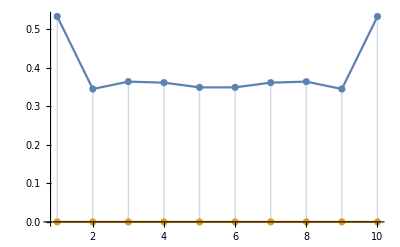

```mathematica
Do[
Do[M[[i,i+n]]=N[d[[i]]],{i,n}];
Do[M[[i+n,i]]=N[Conjugate[d[[i]]]],{i,n}];

{e,evec}=Eigensystem[M];
{evecU,evecV}=Partition[evecᵀ,n];

(*d=0.5 V (evecU evecV*).Tanh[0.5/T e];*)
d=-V (evecU evecV*).(1/(Exp[e/T]+1));
,{iter,1000}]//AbsoluteTiming

ndens=Table[Sum[(evec[[k,i]]^2 1/(Exp[e[[k]]/T]+1)+evec[[k,i+n]]^2 1/(Exp[-e[[k]]/T]+1)),{k,2 n}],{i,n}];
-T Total@Log[1+Exp[-(Abs@e/T)]]-Sum[(d[[i]] d[[i]]*)/V,{i,n}]
(*Show[{ListLinePlot[Abs@d,PlotRange->All],ListPlot[Abs@d,Filling->Axis]}]*)
Show[{ListLinePlot[{Re@d,Im@d},PlotRange->All],ListPlot[{Re@d,Im@d},Filling->Axis]}]
```

```mathematica
d/Emax
```

{0.071168,0.0460455,0.0485843,0.0482405,0.046605,0.046605,0.0482405,0.0485843,0.0460455,0.071168}

100^3 time in days

```mathematica
653 100  100/3600/24//N
%/30
```

75.5787

2.51929

50^3 time in hours

```mathematica
11.894782 100  100/3600//N
%/30
```

33.0411

1.10137

```mathematica
10000/250
```

40

```mathematica
2^(17/3)//N
```

50.7968

```mathematica
0.5 2^14/3600/24//N
```

0.0948148

20^3 time in hours

```mathematica
0.338539 100  100/3600//N
```

0.940386

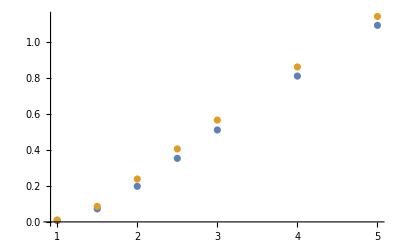

```mathematica
Tsurf={{1,0.011},{1.5,0.086},{2,0.238},{2.5,0.405},{3,0.565},{4,0.86},{5,1.14}};
ListPlot[{Tcs,Tsurf},PlotRange->All]
```

```mathematica
Tcs={{1.,0.0074529900550842285},{1.5,0.07237853145599366},{2.,0.1975286955833435},{2.5,0.35267929840087886},{3.,0.5101834397315979},{4.,0.8091533827781678},{5.,1.0907214589118959}};
```

{{1.,0.475918},{1.5,0.188198},{2.,0.204888},{2.5,0.148352},{3.,0.107445},{4.,0.0628393},{5.,0.0451798}}

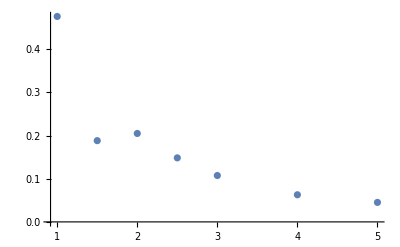

```mathematica
dT=Table[{Tcs[[i,1]],(Tsurf[[i,2]]-Tcs[[i,2]])/Tcs[[i,2]]},{i,Length@Tcs}]
ListPlot[dT,PlotRange->All]
```

# Anal Tc bulk

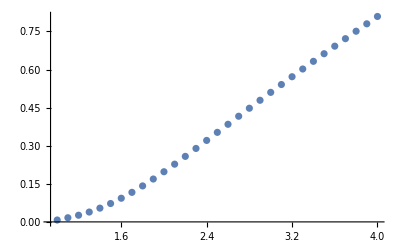

```mathematica
V=2;
μ=0.5;
t=1;
n=100;

Tcs={};

Do[

TN=V 1/4;
TSC=0.001;

e[q_,da_]=√(da^2+(2 t Cos[π/(n+1) q]+μ)^2);

Do[
TQ=(TN+TSC)/2;
If[Abs[da/.FindRoot[V/4 2/(n+1) Sum[1/e[q,da] Tanh[e[q,da]/(2 TQ)],{q,1,n}]==1,{da,0.1}]]>10^-5,TSC=TQ,TN=TQ]
,{iter,20}]//Quiet;

AppendTo[Tcs,{V,(TN+TSC)/2}];

,{V,1,4,0.1}]
ListPlot[Tcs,PlotRange->All]
```

```mathematica
Tcs={{1.,0.0074529900550842285},{1.1,0.01636026477813721},{1.2,0.02627543115615845},{1.3,0.038819662094116206},{1.4,0.05420774221420289},{1.5,0.07237853145599366},{1.6,0.09317335462570192},{1.7000000000000002,0.11637079238891601},{1.8,0.14170194768905642},{1.9,0.16886317157745362},{2.,0.1975286955833435},{2.1,0.22736583518981934},{2.2,0.2580570969581604},{2.3,0.28932117176055916},{2.4000000000000004,0.32092307710647583},{2.5,0.35267929840087886},{2.6,0.38445259523391717},{2.7,0.41614523029327394},{2.8,0.4476906218528748},{2.9000000000000004,0.47904530143737795},{3.,0.5101834397315979},{3.1,0.5410914182662964},{3.2,0.5717620186805723},{3.3000000000000003,0.6021962547302246},{3.4000000000000004,0.6323984894752503},{3.5,0.6623733377456665},{3.6,0.6921299986839294},{3.7,0.7216770153045657},{3.8000000000000003,0.7510244641304014},{3.9000000000000004,0.7801792860031129},{4.,0.8091533827781678}};
```

-0.345424+0.285047 x

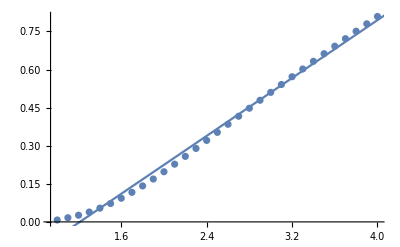

```mathematica
fit=a x+b/.FindFit[Tcs,a x+b,{a,b},x]
Show[{ListPlot[Tcs,PlotRange->All],Plot[fit,{x,0,10}]}]
```

# Matrix estimations

```mathematica
T=0.1;
h=0;
H=0;

n=10;
t[i_]=t0 Exp[ⅈ H i];
Do[μ[i]=μ0 ;,{i,n}];
V=2.0;
periodic=0;
hpm[i_,j_,sign_]=(t[i] KroneckerDelta[i,j+1]+t[j] KroneckerDelta[i,j-1]+periodic t[i] (KroneckerDelta[i,1] KroneckerDelta[j,n]+KroneckerDelta[i,n] KroneckerDelta[j,1]))-(μ[i]+sign h) KroneckerDelta[i,j];
d=Table[Δ[i],{i,n}];
M=Table[0,{i,2 n},{j,2 n}];

Do[M[[i,j]]=hpm[i,j,(+1)],{i,n},{j,n}];
Do[M[[i+n,j+n]]=-hpm[i,j,(-1)],{i,n},{j,n}];
```

```mathematica
h=Table[If[i==n+5,1,0],{i,1,2 n}];
```

```mathematica
Do[M[[i,i+n]]=d[[i]],{i,n}];
Do[M[[i+n,i]]=d[[i]],{i,n}];
```

```mathematica
M.M.M.M.h//MatrixForm
```

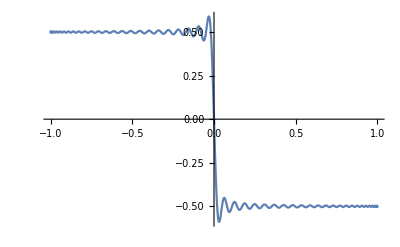

```mathematica
mat=M;
data={};
Do[
non0=0;
Do[If[mat[[i,j]]≠0,non0++],{i,2 n},{j,2 n}];
mat=mat.M;
AppendTo[data,{iter,non0/(2 n)^2//N}];
,{iter,1,10}]
ListPlot[data,PlotRange->All]
```